# Mathematica Lab 1-Properties Fourier Series Representation

## Property-Time Shifting of a Continuous-Time Periodic Signal (with general explanations) *SCIMATH301 - Signals & Systems* *Joanikij Chulev* *22.09.2022*

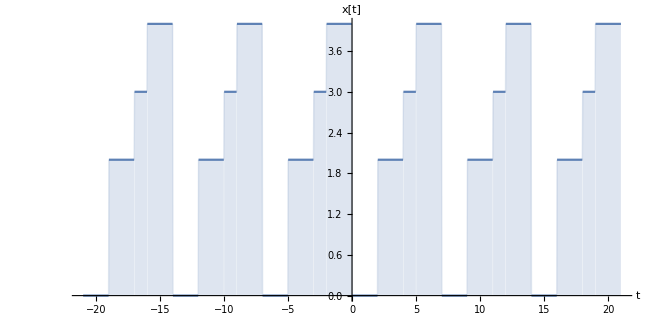

```mathematica
(* This defines the period and each period is also piecewise: *)T=7;
(* This defines a piecewise periodic continuous-time signal: *)
x[t_]:=Piecewise[{{0,0≤Mod[t,T]<2},{2,2≤Mod[t,T]<4},{3,4≤Mod[t,T]<5},{4,5≤Mod[t,T]≤7}}];
(* This plots 6 periods of the periodic signal: *)
Px=Plot[x[t],{t,-3T,3T},PlotRange->All,AspectRatio->1/2,Filling->Axis,AxesLabel->{"t","x[t]"}]
```

(ⅇ^(-2 ⅈ k π) (2 ⅈ-2 ⅈ ⅇ^((4 ⅈ k π)/7)+ⅈ ⅇ^((6 ⅈ k π)/7)-ⅈ ⅇ^((10 ⅈ k π)/7)+3 ⅇ^((5 ⅈ k π)/7) Sin[(k π)/7]))/(k π)

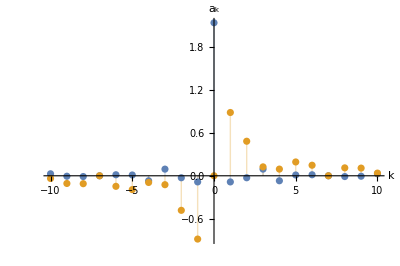

```mathematica
(* This calculates the Fourier Series coefficients: *)
a[k_]=1/T∫_0^T x[t]Exp[-ⅉ k (2π)/T t]ⅆt
(* This is a table of ak's: *)
val=Table[{k,If[k≠0,a[k],Limit[a[kk],kk->0]]},{k,-10,10}];
(* This plots the real and imaginary part of the ak's: *)
Pak=ListPlot[{Transpose[{Transpose[val][[1]],Re[Transpose[val][[2]]]}],Transpose[{Transpose[val][[1]],Im[Transpose[val][[2]]]}]},PlotRange->All,Filling->Axis,AspectRatio->2/3,AxesLabel->{"k","a_k"}]
```

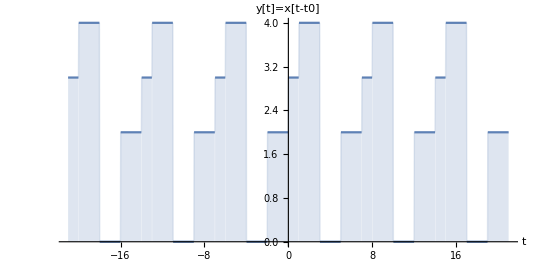

```mathematica
(* THIS IMPLEMENTS THE TIME SHIFTING *)
(* X[t-t0] *)
t0:=-4; 
y[t_]:=x[t-t0];
Py=Plot[y[t],{t,-3T,3T},PlotRange->All,AspectRatio->1/2,Filling->Axis,AxesLabel->{"t","y[t]=x[t-t0]"}]
```

-(ⅈ ⅇ^(-2 ⅈ k π) (-2+2 ⅇ^((4 ⅈ k π)/7)-4 ⅇ^((8 ⅈ k π)/7)+ⅇ^((12 ⅈ k π)/7)+3 ⅇ^(2 ⅈ k π)))/(2 k π)

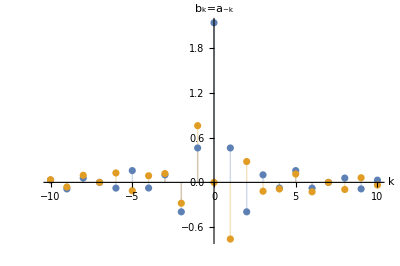

```mathematica
(* This calculates the Fourier Series coefficients: *)
b[k_]=1/T∫_0^T y[t]Exp[-ⅉ k (2π)/T t]ⅆt
(* This is a table of ak's: *)
val2=Table[{k,If[k≠0,b[k],Limit[b[kk],kk->0]]},{k,-10,10}];
(* This plots the real and imaginary part of the ak's: *)
Pbk=ListPlot[{Transpose[{Transpose[val2][[1]],Re[Transpose[val2][[2]]]}],Transpose[{Transpose[val2][[1]],Im[Transpose[val2][[2]]]}]},PlotRange->All,Filling->Axis,AspectRatio->2/3,AxesLabel->{"k","b_k=a_-k"}]
```

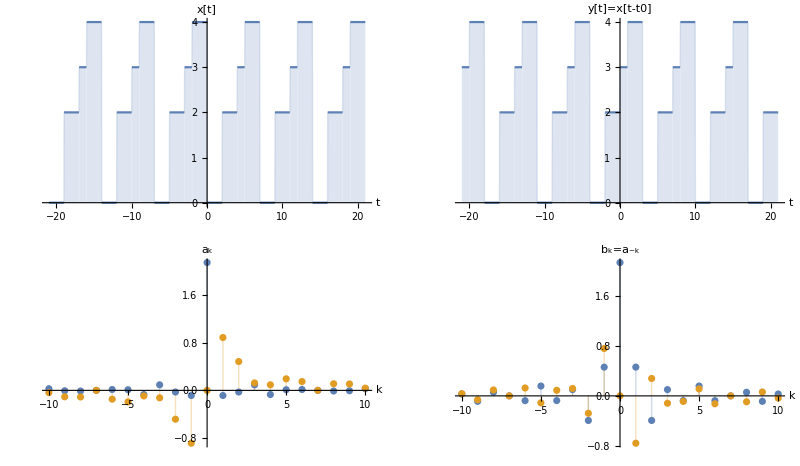

```mathematica
(* This shows all plots in one overview: *)
GraphicsGrid[{{Px,Py},{Pak,Pbk}},Frame->True]
```